```mathematica
ClearAll["Global`*"]
SetOptions[EvaluationNotebook[],Background->LightGray]
SetDirectory["/Users/spencerbryngelson/Desktop/Fortran/EV_spectral/D"];
data=Import[#,"Table"]&/@FileNames["eval*"];
Table[vec[j]=data[[j]],{j,1,Length[data]}];
```

```mathematica
Do[ReEv[i]=Table[vec[i][[j,1]],{j,1,Length[vec[i]]}],{i,1,Length[data]}]
Do[SortReEv1[i]=Drop[Sort[ReEv[i]],-1],{i,1,Length[data]}]
Do[SortReEv2[i]=Drop[Sort[ReEv[i]],-2],{i,1,Length[data]}]
Do[SortReEv3[i]=Drop[Sort[ReEv[i]],-3],{i,1,Length[data]}]
Do[SortReEv4[i]=Drop[Sort[ReEv[i]],-4],{i,1,Length[data]}]
Do[
Do[SortReEv[i,j]=Drop[Sort[ReEv[i]],-j],{i,1,Length[data]}],
{j,0,10}]
```

```mathematica
Do[MaxEv[i]=Max[ReEv[i]],{i,1,Length[data]}]
Do[MaxEv1[i]=Max[SortReEv1[i]],{i,1,Length[data]}]
Do[MaxEv2[i]=Max[SortReEv2[i]],{i,1,Length[data]}]
Do[MaxEv3[i]=Max[SortReEv3[i]],{i,1,Length[data]}]
Do[MaxEv4[i]=Max[SortReEv4[i]],{i,1,Length[data]}]
Do[
Do[SortMaxEv[i,j]=Max[SortReEv[i,j]],{i,1,Length[data]}]
,{j,0,10}]
```

```mathematica
R1=1.0;
R2=Table[i/10.,{i,1,50,2}];
```

```mathematica
xs=R1/(R1+R2);
ys=Table[MaxEv[i],{i,1,Length[data]}];
ys1=Table[MaxEv1[i],{i,1,Length[data]}];
ys2=Table[MaxEv2[i],{i,1,Length[data]}];
ys3=Table[MaxEv3[i],{i,1,Length[data]}];
ys4=Table[MaxEv4[i],{i,1,Length[data]}];
pairs=Thread[{xs,ys}];
pairs1=Thread[{xs,ys1}];
pairs2=Thread[{xs,ys2}];
pairs3=Thread[{xs,ys3}];
pairs4=Thread[{xs,ys4}];
```

```mathematica
xs
```

{0.909091,0.769231,0.666667,0.588235,0.526316,0.47619,0.434783,0.4,0.37037,0.344828,0.322581,0.30303,0.285714,0.27027,0.25641,0.243902,0.232558,0.222222,0.212766,0.204082,0.196078,0.188679,0.181818,0.175439,0.169492}

```mathematica
Do[
SortPairs[j]=Thread[{xs,Table[SortMaxEv[i,j],{i,1,Length[data]}]}]
,{j,0,10}]
```

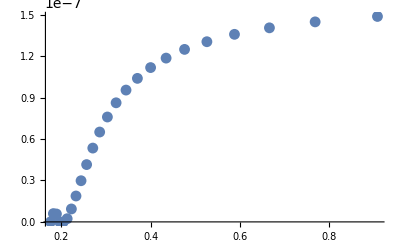
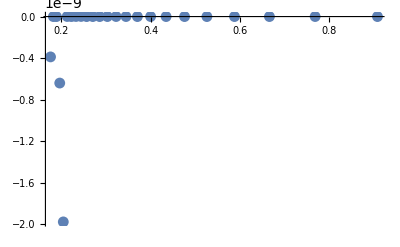
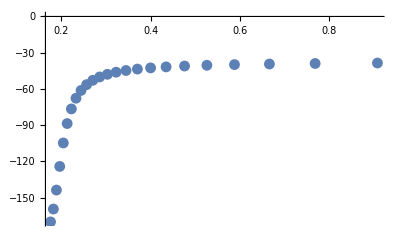
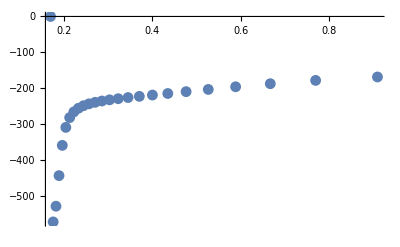
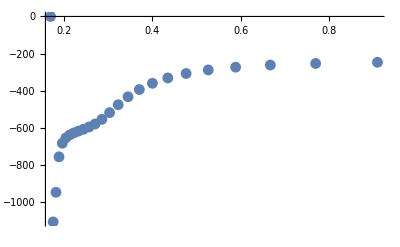
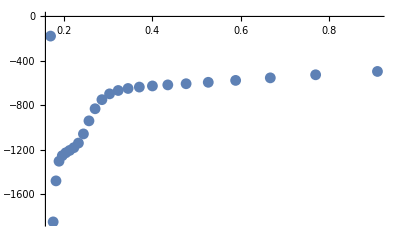
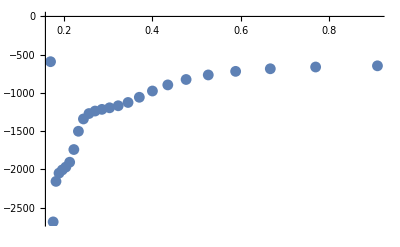
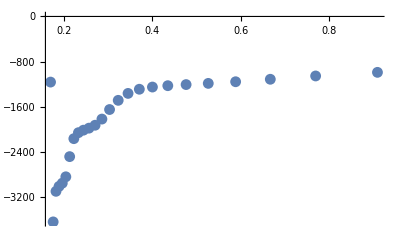

```mathematica
Table[ListPlot[SortPairs[j],PlotRange->All],{j,0,10}]
```

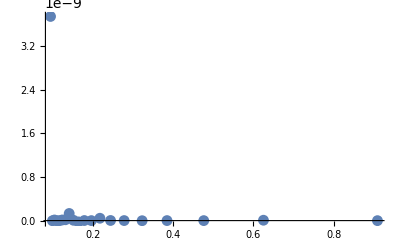

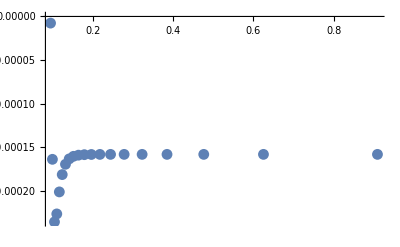

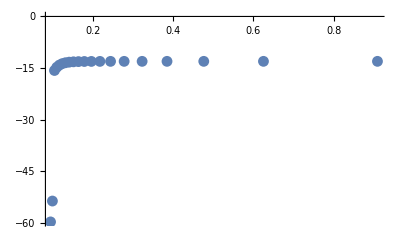

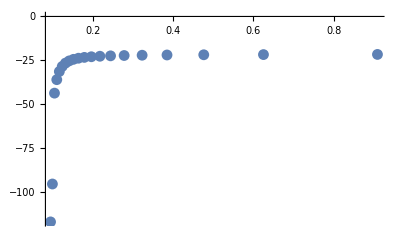

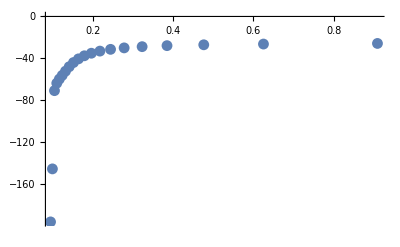

```mathematica
ListPlot[pairs,PlotRange->All]
ListPlot[pairs1,PlotRange->All]
ListPlot[pairs2,PlotRange->All]
ListPlot[pairs3,PlotRange->All]
ListPlot[pairs4,PlotRange->All]
```

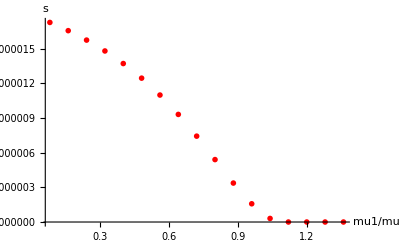

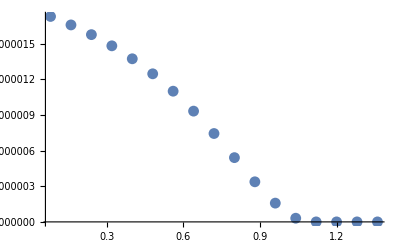

```mathematica
l1=ListPlot[pairs,Joined->False,PlotRange->All,PlotStyle->{PointSize[0.01],Red},AxesLabel->{"mu1/mu2","s"},LabelStyle->Directive[14]]
```

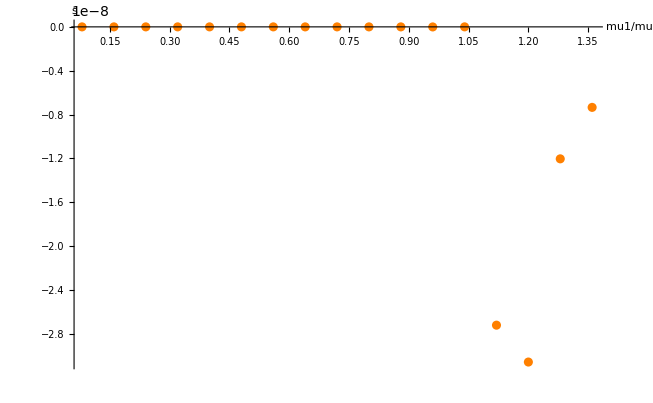

```mathematica
l3=ListPlot[pairs1,Joined->False,PlotRange->All,PlotStyle->{PointSize[0.01],Orange},AxesLabel->{"mu1/mu2","s"},LabelStyle->Directive[14]]
```

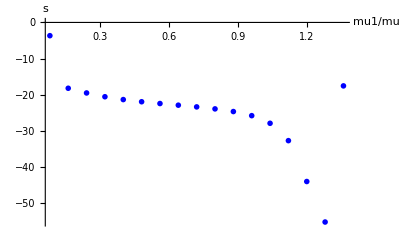

```mathematica
l2=ListPlot[pairs2,Joined->False,PlotRange->All,PlotStyle->{PointSize[0.01],Blue},AxesLabel->{"mu1/mu2","s"},LabelStyle->Directive[14]]
```

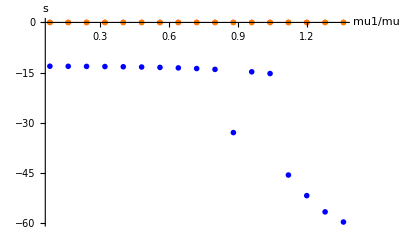

```mathematica
Show[l1,l2,l3,PlotRange->All]
```

```mathematica
SetDirectory["/Users/spencerbryngelson/Desktop/Fortran/EV_Spectral/V"]
```

/Users/spencerbryngelson/Desktop/Fortran/EV_spectral/V

```mathematica
ClearAll["Global`*"]
```

```mathematica
data=Import[#,"Table"]&/@FileNames["x.*"];
```

```mathematica
Table[vec[j]=data[[j]],{j,1,Length[data]}];
Table[realvec[i]=Table[vec[i][[j,1]],{j,1,Length[data]}],{i,1,Length[data]}];
Table[imvec[i]=Table[vec[i][[j,2]],{j,1,Length[data]}],{i,1,Length[data]}];
```

```mathematica
Dimensions[data]
```

{60,60,2}

```mathematica
Length[data]
```

60

```mathematica
(* only first two have true nonzero eigenvalues *)
```

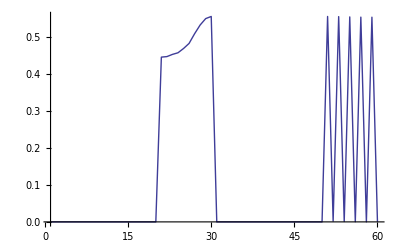
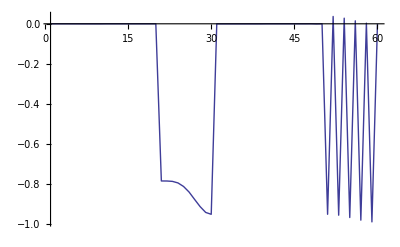
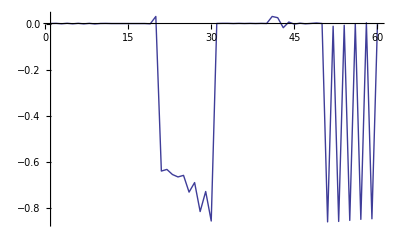
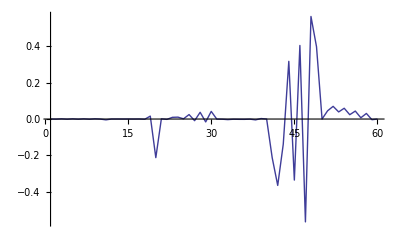
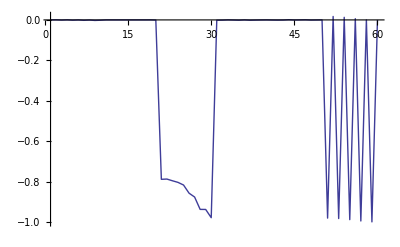
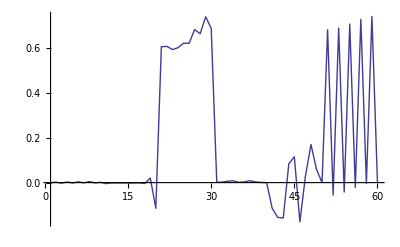
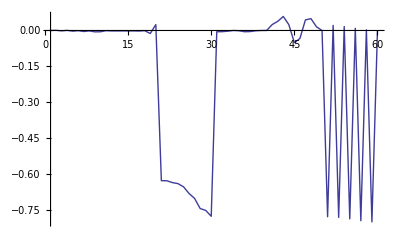
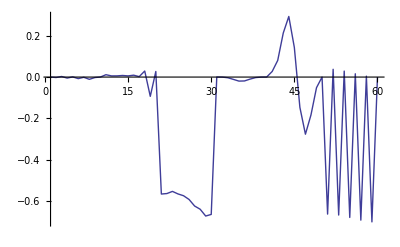

```mathematica
Table[ListPlot[realvec[j],PlotRange->All,Joined->True],{j,1,Length[data]}]
```

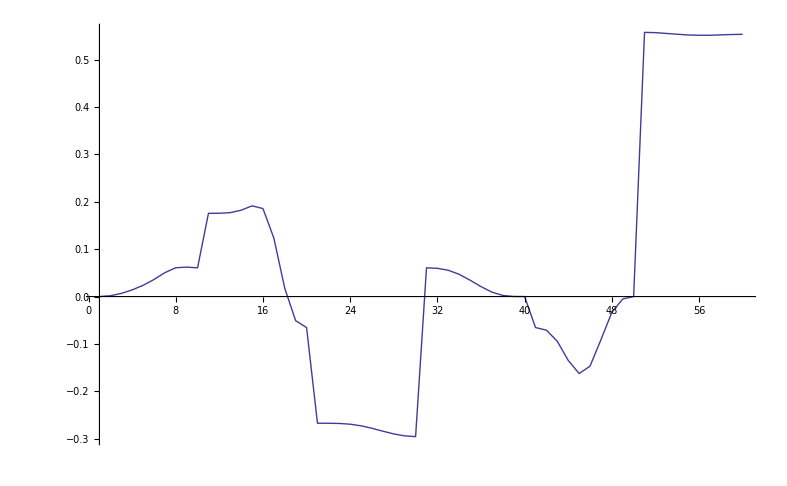

```mathematica
ListPlot[realvec[10],PlotRange->All,Joined->True]
```

```mathematica
(4*100000)/(60.*60*24)
```

4.62963

```mathematica
14.*60*60/6000
```

8.4